```mathematica
np=1.785;nr=1.64;ϕ1=68*Pi/180;ϕ2=68*Pi/180;θ1=90*Pi/180;θ2=90*Pi/180;λ=405*10^-9;
kx = 2Pi*np*Sin[ϕ1]*Cos[θ1]/λ 
kx2 = 2Pi*np*Sin[ϕ2]*Cos[θ2]/λ 
ky = 2Pi*np*Sin[ϕ1]*Sin[θ1]/λ 
ky2 = -2Pi*np*Sin[ϕ2]*Sin[θ2]/λ 
kz = 2Pi*np*Sqrt[(Sin[ϕ1])^2-nr^2/np^2]/λ 
kz2 = 2Pi*np*Sqrt[(Sin[ϕ2])^2-nr^2/np^2]/λ 
evanescent[ x_,y_, z_] = E02 Exp[I (kx*x + ky*y)-Abs[kz] Abs[z]]+E01 Exp[I (kx2*x + ky2*y)-Abs[kz2]Abs[z]]//.{E01-> 1,E02-> 1}
evanescent2d[ y_, z_] = E02 Exp[I (ky*y)-Abs[kz] Abs[z]]+E01 Exp[I (ky2*y)-Abs[kz2]Abs[z]]//.{E01-> 1,E02-> 1}
```

0.

0.

2.56761×10^7

-2.56761×10^7

3.45172×10^6

3.45172×10^6

ⅇ^(ⅈ (0.-2.56761×10^7 y)-3.45172×10^6 Abs[z])+ⅇ^(ⅈ (0.+2.56761×10^7 y)-3.45172×10^6 Abs[z])

ⅇ^((0.-2.56761×10^7 ⅈ) y-3.45172×10^6 Abs[z])+ⅇ^((0.+2.56761×10^7 ⅈ) y-3.45172×10^6 Abs[z])

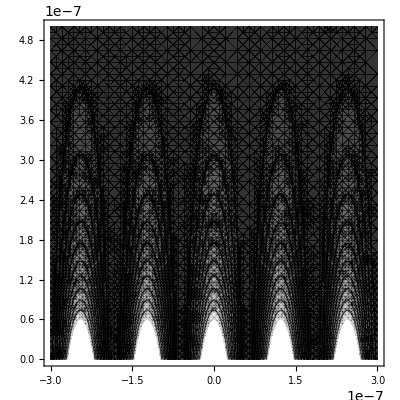

```mathematica
ContourPlot[N[evanescent2d[y,z] Conjugate[evanescent2d[y,z]],8],{y,-0.3/10^6,0.3/10^6},{z,0,0.5/10^6},PlotTheme->"Monochrome",Contours->10]
```

```mathematica
ContourPlot3D[N[evanescent[x,y,z] Conjugate[evanescent[x,y,z]],8],{x,-0.3/10^6,0.3/10^6},{y,-0.3/10^6,0.3/10^6},{z,0,0.5/10^6},PlotTheme->"Monochrome",Contours->10]
```

-Graphics3D-